```mathematica
Grid[Table[First[Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[MinimalGraph[k]]]],{k,5,20}]]
```

2 | 2 | 1 | 1
3 | 2 | 1 | 1
3 | 3 | 1 | 1
4 | 3 | 1 | 1
4 | 4 | 1 | 1
5 | 4 | 1 | 1
5 | 5 | 1 | 1
6 | 5 | 1 | 1
6 | 6 | 1 | 1
7 | 6 | 1 | 1
7 | 7 | 1 | 1
8 | 7 | 1 | 1
8 | 8 | 1 | 1
9 | 8 | 1 | 1
9 | 9 | 1 | 1
10 | 9 | 1 | 1

```mathematica
TableForm[Table[Sort[Tally[Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[JacobsThalGraph[k]]]]],{k,4,6}], TableDepth->1]
```

{{{2,2,2,2},4},{{3,2,2,1},6},{{3,3,1,1},1}}
{{{3,2,2,2},14},{{3,3,2,1},7}}
{{{3,3,2,2},28},{{4,2,2,2},6},{{4,3,2,1},8},{{4,4,1,1},1}}

```mathematica
IntegerPartitions[7,{4}]//Sort//Grid
```

2 | 2 | 2 | 1
3 | 2 | 1 | 1
4 | 1 | 1 | 1

```mathematica
IntegerPartitions[8,{4}]//Sort//Grid
```

2 | 2 | 2 | 2
3 | 2 | 2 | 1
3 | 3 | 1 | 1
4 | 2 | 1 | 1
5 | 1 | 1 | 1

```mathematica
IntegerPartitions[9,{4}]//Sort//Grid
```

3 | 2 | 2 | 2
3 | 3 | 2 | 1
4 | 2 | 2 | 1
4 | 3 | 1 | 1
5 | 2 | 1 | 1
6 | 1 | 1 | 1

```mathematica
Table[
Labeled[IntegerPartitions[k,{4}]//Sort//Grid,Style[k,Red,Bold]],
{k,7,15}
]
```

{2 | 2 | 2 | 1
3 | 2 | 1 | 1
4 | 1 | 1 | 17,2 | 2 | 2 | 2
3 | 2 | 2 | 1
3 | 3 | 1 | 1
4 | 2 | 1 | 1
5 | 1 | 1 | 18,3 | 2 | 2 | 2
3 | 3 | 2 | 1
4 | 2 | 2 | 1
4 | 3 | 1 | 1
5 | 2 | 1 | 1
6 | 1 | 1 | 19,3 | 3 | 2 | 2
3 | 3 | 3 | 1
4 | 2 | 2 | 2
4 | 3 | 2 | 1
4 | 4 | 1 | 1
5 | 2 | 2 | 1
5 | 3 | 1 | 1
6 | 2 | 1 | 1
7 | 1 | 1 | 110,3 | 3 | 3 | 2
4 | 3 | 2 | 2
4 | 3 | 3 | 1
4 | 4 | 2 | 1
5 | 2 | 2 | 2
5 | 3 | 2 | 1
5 | 4 | 1 | 1
6 | 2 | 2 | 1
6 | 3 | 1 | 1
7 | 2 | 1 | 1
8 | 1 | 1 | 111,3 | 3 | 3 | 3
4 | 3 | 3 | 2
4 | 4 | 2 | 2
4 | 4 | 3 | 1
5 | 3 | 2 | 2
5 | 3 | 3 | 1
5 | 4 | 2 | 1
5 | 5 | 1 | 1
6 | 2 | 2 | 2
6 | 3 | 2 | 1
6 | 4 | 1 | 1
7 | 2 | 2 | 1
7 | 3 | 1 | 1
8 | 2 | 1 | 1
9 | 1 | 1 | 112,4 | 3 | 3 | 3
4 | 4 | 3 | 2
4 | 4 | 4 | 1
5 | 3 | 3 | 2
5 | 4 | 2 | 2
5 | 4 | 3 | 1
5 | 5 | 2 | 1
6 | 3 | 2 | 2
6 | 3 | 3 | 1
6 | 4 | 2 | 1
6 | 5 | 1 | 1
7 | 2 | 2 | 2
7 | 3 | 2 | 1
7 | 4 | 1 | 1
8 | 2 | 2 | 1
8 | 3 | 1 | 1
9 | 2 | 1 | 1
10 | 1 | 1 | 113,4 | 4 | 3 | 3
4 | 4 | 4 | 2
5 | 3 | 3 | 3
5 | 4 | 3 | 2
5 | 4 | 4 | 1
5 | 5 | 2 | 2
5 | 5 | 3 | 1
6 | 3 | 3 | 2
6 | 4 | 2 | 2
6 | 4 | 3 | 1
6 | 5 | 2 | 1
6 | 6 | 1 | 1
7 | 3 | 2 | 2
7 | 3 | 3 | 1
7 | 4 | 2 | 1
7 | 5 | 1 | 1
8 | 2 | 2 | 2
8 | 3 | 2 | 1
8 | 4 | 1 | 1
9 | 2 | 2 | 1
9 | 3 | 1 | 1
10 | 2 | 1 | 1
11 | 1 | 1 | 114,4 | 4 | 4 | 3
5 | 4 | 3 | 3
5 | 4 | 4 | 2
5 | 5 | 3 | 2
5 | 5 | 4 | 1
6 | 3 | 3 | 3
6 | 4 | 3 | 2
6 | 4 | 4 | 1
6 | 5 | 2 | 2
6 | 5 | 3 | 1
6 | 6 | 2 | 1
7 | 3 | 3 | 2
7 | 4 | 2 | 2
7 | 4 | 3 | 1
7 | 5 | 2 | 1
7 | 6 | 1 | 1
8 | 3 | 2 | 2
8 | 3 | 3 | 1
8 | 4 | 2 | 1
8 | 5 | 1 | 1
9 | 2 | 2 | 2
9 | 3 | 2 | 1
9 | 4 | 1 | 1
10 | 2 | 2 | 1
10 | 3 | 1 | 1
11 | 2 | 1 | 1
12 | 1 | 1 | 115}

```mathematica
TableForm[Table[{k,Sort[Tally[Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[Graph[plantri[[k]]]]]]]},{k,1,22}],TableDepth->1]
```

{1,{{{3,3,3,3},10}}}
{2,{{{4,4,3,3},19},{{4,4,4,2},1}}}
{3,{{{4,4,4,3},32}}}
{4,{{{4,4,4,4},30}}}
{5,{{{4,4,4,4},27}}}
{6,{{{4,4,4,4},42}}}
{7,{{{5,4,4,4},16}}}
{8,{{{5,4,4,4},20},{{5,5,4,3},2}}}
{9,{{{5,4,4,4},32}}}
{10,{{{5,4,4,4},20},{{5,5,4,3},20}}}
{11,{{{5,5,4,4},36},{{5,5,5,3},8}}}
{12,{{{5,5,4,4},30}}}
{13,{{{5,5,4,4},44},{{5,5,5,3},4}}}
{14,{{{5,5,4,4},34},{{5,5,5,3},4}}}
{15,{{{5,5,4,4},52}}}
{16,{{{5,5,4,4},51},{{5,5,5,3},2}}}
{17,{{{5,5,4,4},30},{{5,5,5,3},4}}}
{18,{{{5,5,4,4},48},{{6,4,4,4},16}}}
{19,{{{5,5,4,4},70},{{5,5,5,3},8}}}
{20,{{{5,5,4,4},49},{{5,5,5,3},4}}}
{21,{{{5,5,4,4},48}}}
{22,{{{5,5,4,4},52}}}

```mathematica
Table[{k,VertexCount[Graph[plantri[[k]]]]},{k,500}]
```

{{1,12},{2,14},{3,15},{4,16},{5,16},{6,16},{7,17},{8,17},{9,17},{10,17},{11,18},{12,18},{13,18},{14,18},{15,18},{16,18},{17,18},{18,18},{19,18},{20,18},{21,18},{22,18},{23,19},{24,19},{25,19},{26,19},{27,19},{28,19},{29,19},{30,19},{31,19},{32,19},{33,19},{34,19},{35,19},{36,19},{37,19},{38,19},{39,19},{40,19},{41,19},{42,19},{43,19},{44,19},{45,19},{46,20},{47,20},{48,20},{49,20},{50,20},{51,20},{52,20},{53,20},{54,20},{55,20},{56,20},{57,20},{58,20},{59,20},{60,20},{61,20},{62,20},{63,20},{64,20},{65,20},{66,20},{67,20},{68,20},{69,20},{70,20},{71,20},{72,20},{73,20},{74,20},{75,20},{76,20},{77,20},{78,20},{79,20},{80,20},{81,20},{82,20},{83,20},{84,20},{85,20},{86,20},{87,20},{88,20},{89,20},{90,20},{91,20},{92,20},{93,20},{94,20},{95,20},{96,20},{97,20},{98,20},{99,20},{100,20},{101,20},{102,20},{103,20},{104,20},{105,20},{106,20},{107,20},{108,20},{109,20},{110,20},{111,20},{112,20},{113,20},{114,20},{115,20},{116,20},{117,20},{118,20},{119,21},{120,21},{121,21},{122,21},{123,21},{124,21},{125,21},{126,21},{127,21},{128,21},{129,21},{130,21},{131,21},{132,21},{133,21},{134,21},{135,21},{136,21},{137,21},{138,21},{139,21},{140,21},{141,21},{142,21},{143,21},{144,21},{145,21},{146,21},{147,21},{148,21},{149,21},{150,21},{151,21},{152,21},{153,21},{154,21},{155,21},{156,21},{157,21},{158,21},{159,21},{160,21},{161,21},{162,21},{163,21},{164,21},{165,21},{166,21},{167,21},{168,21},{169,21},{170,21},{171,21},{172,21},{173,21},{174,21},{175,21},{176,21},{177,21},{178,21},{179,21},{180,21},{181,21},{182,21},{183,21},{184,21},{185,21},{186,21},{187,21},{188,21},{189,21},{190,21},{191,21},{192,21},{193,21},{194,21},{195,21},{196,21},{197,21},{198,21},{199,21},{200,21},{201,21},{202,21},{203,21},{204,21},{205,21},{206,21},{207,21},{208,21},{209,21},{210,21},{211,21},{212,21},{213,21},{214,21},{215,21},{216,21},{217,21},{218,21},{219,21},{220,21},{221,21},{222,21},{223,21},{224,21},{225,21},{226,21},{227,21},{228,21},{229,21},{230,21},{231,21},{232,21},{233,21},{234,21},{235,21},{236,21},{237,21},{238,21},{239,21},{240,21},{241,21},{242,21},{243,21},{244,21},{245,21},{246,21},{247,21},{248,21},{249,21},{250,21},{251,21},{252,21},{253,21},{254,21},{255,21},{256,21},{257,21},{258,21},{259,21},{260,21},{261,21},{262,21},{263,21},{264,21},{265,21},{266,21},{267,21},{268,21},{269,21},{270,21},{271,21},{272,21},{273,21},{274,21},{275,21},{276,21},{277,21},{278,21},{279,21},{280,21},{281,21},{282,21},{283,21},{284,21},{285,21},{286,21},{287,21},{288,21},{289,21},{290,21},{291,21},{292,21},{293,21},{294,21},{295,21},{296,21},{297,21},{298,21},{299,21},{300,21},{301,21},{302,21},{303,21},{304,21},{305,21},{306,21},{307,21},{308,21},{309,21},{310,21},{311,22},{312,22},{313,22},{314,22},{315,22},{316,22},{317,22},{318,22},{319,22},{320,22},{321,22},{322,22},{323,22},{324,22},{325,22},{326,22},{327,22},{328,22},{329,22},{330,22},{331,22},{332,22},{333,22},{334,22},{335,22},{336,22},{337,22},{338,22},{339,22},{340,22},{341,22},{342,22},{343,22},{344,22},{345,22},{346,22},{347,22},{348,22},{349,22},{350,22},{351,22},{352,22},{353,22},{354,22},{355,22},{356,22},{357,22},{358,22},{359,22},{360,22},{361,22},{362,22},{363,22},{364,22},{365,22},{366,22},{367,22},{368,22},{369,22},{370,22},{371,22},{372,22},{373,22},{374,22},{375,22},{376,22},{377,22},{378,22},{379,22},{380,22},{381,22},{382,22},{383,22},{384,22},{385,22},{386,22},{387,22},{388,22},{389,22},{390,22},{391,22},{392,22},{393,22},{394,22},{395,22},{396,22},{397,22},{398,22},{399,22},{400,22},{401,22},{402,22},{403,22},{404,22},{405,22},{406,22},{407,22},{408,22},{409,22},{410,22},{411,22},{412,22},{413,22},{414,22},{415,22},{416,22},{417,22},{418,22},{419,22},{420,22},{421,22},{422,22},{423,22},{424,22},{425,22},{426,22},{427,22},{428,22},{429,22},{430,22},{431,22},{432,22},{433,22},{434,22},{435,22},{436,22},{437,22},{438,22},{439,22},{440,22},{441,22},{442,22},{443,22},{444,22},{445,22},{446,22},{447,22},{448,22},{449,22},{450,22},{451,22},{452,22},{453,22},{454,22},{455,22},{456,22},{457,22},{458,22},{459,22},{460,22},{461,22},{462,22},{463,22},{464,22},{465,22},{466,22},{467,22},{468,22},{469,22},{470,22},{471,22},{472,22},{473,22},{474,22},{475,22},{476,22},{477,22},{478,22},{479,22},{480,22},{481,22},{482,22},{483,22},{484,22},{485,22},{486,22},{487,22},{488,22},{489,22},{490,22},{491,22},{492,22},{493,22},{494,22},{495,22},{496,22},{497,22},{498,22},{499,22},{500,22}}

```mathematica
TableForm[Sort[Tally[Map[{Total[#],#}&,Flatten[Table[Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[Graph[plantri[[k]]]]],{k,1,22}],1]]]], TableDepth->1]
```

{{12,{3,3,3,3}},10}
{{14,{4,4,3,3}},19}
{{14,{4,4,4,2}},1}
{{15,{4,4,4,3}},32}
{{16,{4,4,4,4}},99}
{{17,{5,4,4,4}},88}
{{17,{5,5,4,3}},22}
{{18,{5,5,4,4}},544}
{{18,{5,5,5,3}},34}
{{18,{6,4,4,4}},16}

```mathematica
Monitor[TableForm[Sort[Tally[Map[{Total[#],#}&,Flatten[Table[Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[Graph[plantri[[k]]]]],{k,1,118}],1]]]], TableDepth->1],k]
```

{{12,{3,3,3,3}},10}
{{14,{4,4,3,3}},19}
{{14,{4,4,4,2}},1}
{{15,{4,4,4,3}},32}
{{16,{4,4,4,4}},99}
{{17,{5,4,4,4}},88}
{{17,{5,5,4,3}},22}
{{18,{5,5,4,4}},544}
{{18,{5,5,5,3}},34}
{{18,{6,4,4,4}},16}
{{19,{5,5,5,4}},1406}
{{19,{6,5,4,4}},136}
{{19,{6,5,5,3}},17}
{{20,{5,5,5,5}},3236}
{{20,{6,5,5,4}},3028}
{{20,{6,6,4,4}},109}
{{20,{6,6,5,3}},51}
{{20,{6,6,6,2}},2}

```mathematica
Monitor[TableForm[Sort[Tally[Map[{Total[#],#}&,Flatten[Table[Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[Graph[plantri[[k]]]]],{k,119,311}],1]]]], TableDepth->1],k]
```

{{21,{6,5,5,5}},15944}
{{21,{6,6,5,4}},5370}
{{21,{6,6,6,3}},80}
{{21,{7,5,5,4}},20}
{{22,{6,6,5,5}},111}
{{22,{6,6,6,4}},25}

```mathematica
MissingEdges3[g_]:=Block[{s,result={}},
Table[
s=Subsets[SymbolToSets[f],{2}];
result={};
Table[
Table[
Table[If[!EdgeQ[g,SortEdge[v1<->v2]],AppendTo[result,SortEdge[v1<->v2]]],
{v2,pairs[[2]]}]
,{v1,pairs[[1]]}],
{pairs,s}
];
f<->DeleteDuplicates[result]
,{f,FindFullFormula4[g]}
]
]
```

```mathematica
MissingEdges3[MinimalGraph[7]]
```

{v1x2x357x468<->{3<->6,3<->8,5<->8,4<->7}}

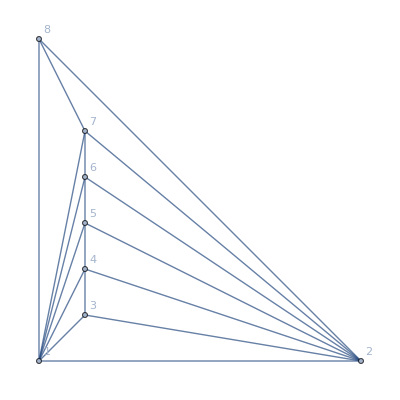

```mathematica
MinimalGraph[7]
```

```mathematica
MissingEdges3[JacobsThalGraph[4]]
```

{v1x257x34x68<->{1<->7,1<->6,1<->8,2<->6,5<->8},v17x26x34x58<->{1<->6,2<->7,1<->8,5<->7,2<->5,6<->8},v17x25x34x68<->{2<->7,5<->7,1<->6,1<->8,2<->6,5<->8},v16x27x34x58<->{1<->7,2<->6,1<->8,6<->8,2<->5,5<->7},v16x257x34x8<->{1<->7,2<->6,1<->8,6<->8,5<->8},v168x2x34x57<->{2<->6,1<->7,5<->8,2<->5,2<->7},v168x27x34x5<->{1<->7,2<->6,5<->8,2<->5,5<->7},v18x26x34x57<->{1<->6,6<->8,1<->7,5<->8,2<->5,2<->7},v168x257x3x4<->{1<->7,2<->6,5<->8,3<->4},v18x257x34x6<->{1<->7,5<->8,1<->6,6<->8,2<->6},v168x25x34x7<->{2<->6,5<->8,1<->7,2<->7,5<->7}}

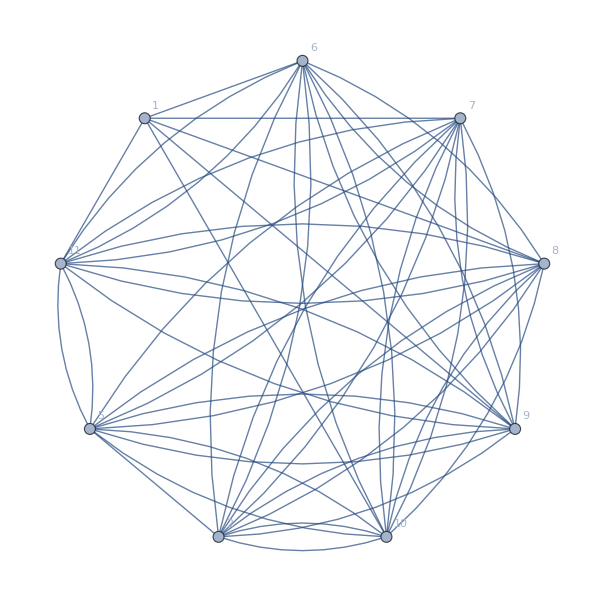

```mathematica
Graph[Map[SortEdge,MissingEdges3[JacobsThalGraph[7]]]//DeleteDuplicates//Sort,GraphLayout->"CircularEmbedding", VertexLabels->"Name"]
```